# Lab 1: Modeling a Ball in Motion Christopher Greene, Erin Murnane, Michael Imbimbo

Consider a spring (k = 10 N/m) with a mass (0.50 kg) attached to  it. Initially the spring 10 cm and the spring is stretched by 10cm and is at rest. Model the behavior of the system over 10s.

### In this example we can write the exact solution to the equation of motion as follows:

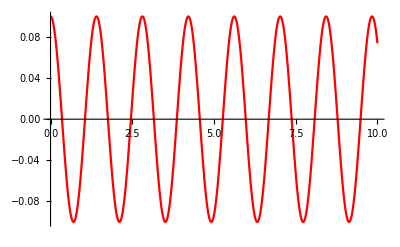

```mathematica
k = 10;
m = 0.50;
ω=√(k/m);
A = 0.1;
exact = A Cos[ω time];
exactplot = Plot[exact,{time,0,10}, PlotStyle -> Red]
```

### Now let's write a numerical procedure to solve the equation of motion and compare with the exact solution

Run the command below and adjust dt to have a sense for what happens as we change the time increment

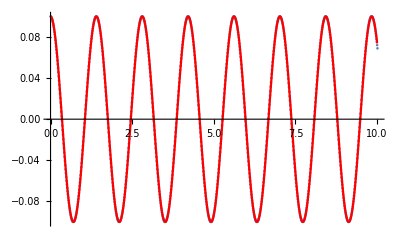

```mathematica
(* define constants and initial conditions *)
k = 10;
m = 0.50;
ω=√(k/m);
x= 0.1;
vx=0;
ti = 0;
tf = 10;
dt = 0.01;

(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
ax = -ω^2 x;

(* redefine y, vy, in terms of the values from the previous step *)

vx = vx + ax dt ;
x = x + vx dt;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,exactplot}]
```